```mathematica
WebImageSearch["Resistor", "Thumbnails"]
```

$Aborted

```mathematica
ColorQuantize[-Graphics-,14]
```

-Graphics-

```mathematica
ColorQuantize[ColorConvert[-Graphics-,"CMYK"],14]
```

-Graphics-

```mathematica
Map[ColorQuantize[#,14]&,WebImageSearch["Resistor", "Thumbnails"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pictures = WebImageSearch["resistor","Thumbnails"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
img = -Graphics-;
saturated = Binarize[ColorConvert[img, "Grayscale"], .9]
Inpaint[img, Dilation[saturated, DiskMatrix[20]]]
```

-Graphics-

-Graphics-

```mathematica
ClearAll[a]
```

```mathematica
ColorQuantize[-Graphics-, 10]
```

-Graphics-

```mathematica
MorphologicalComponents[-Graphics-]//Colorize
```

-Graphics-

```mathematica
lenet=NetChain[
{
ConvolutionLayer[20,5],
Ramp,
PoolingLayer[2,2],
ConvolutionLayer[50,5],
Ramp,
PoolingLayer[2,2],
FlattenLayer[],
500,
Ramp,
10,
SoftmaxLayer[]
},
"Output"->NetDecoder[{"Class",Range[0,9]}],"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}]
]
```

```mathematica
ImageIdentify[-Graphics-]
```

resistor

```mathematica
Entity["Concept","Resistor::d7w57"]["Properties"]
```

{alternate names,broader concepts,definition,equivalent entity,name,narrower concepts,similar entities,subset concepts,superset concepts,WordData senses,WordNet ID}

```mathematica
ImageAlign[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
WebImageSearch["Resistor","Images","MaxItems"->1]
```

{-Graphics-}

```mathematica
DeleteSmallComponents @ChanVeseBinarize[-Graphics-]
```

-Graphics-

```mathematica
HistogramTransform @ ImageAdjust[-Graphics-]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

-Graphics-

```mathematica
ColorQuantize[ImageAdjust[-Graphics-,1],14]
```

-Graphics-

```mathematica
EdgeDetect[-Graphics-]
```

-Graphics-

```mathematica
CrossingDetect[-Graphics-]
```

-Graphics-

```mathematica
ContourDetect[-Graphics-]
```

-Graphics-

```mathematica
img = -Graphics-;
lines = ImageLines[img];
HighlightImage[img, {Orange, Line /@ lines}]
```

-Graphics-

```mathematica
GradientFilter[-Graphics-,1]
```

-Graphics-

```mathematica
img = -Graphics-;
lines = ImageLines[img];
HighlightImage[img, {Orange, Line /@ lines}]
```

-Graphics-

```mathematica
LaplacianGaussianFilter[-Graphics-,1]
```

-Graphics-

```mathematica
img = EdgeDetect[-Graphics-]
lines = ImageLines[img];
HighlightImage[img, {Orange, Line /@ lines}]
```

-Graphics-

-Graphics-

```mathematica
Entity["AdministrativeDivision",{"Massachusetts","UnitedStates"}]["Polygon"]
```

Massachusetts, United States

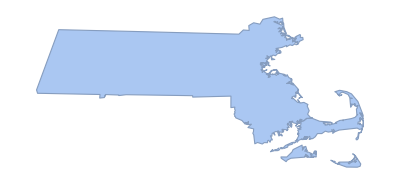

```mathematica
BoundaryDiscretizeGraphics[Entity["AdministrativeDivision",{"Massachusetts","UnitedStates"}]["Polygon"]]
```